# Quantum states of systems of chemical interest using NDEigensystem

Single sentence description of the topic

## 2D-Hydrogen atom

The potential energy

```mathematica
Subscript[V, 2][x_,y_]:=-1/(√(x^2+y^2))
```

The Kinetic energy operator:

```mathematica
Subscript[K, 2][ψ_]:=-1/2∇_{x,y}^2 ψ
```

```mathematica
Subscript[K, 2][ψ[x,y]]
```

1/2 (-ψ^(0,2)[x,y]-ψ^(2,0)[x,y])

The Hamiltonian operator:

```mathematica
Subscript[ℋ, 2][ψ_]:=Subscript[K, 2][ψ]+Subscript[V, 2][x,y]ψ
```

The boundary conditions:

```mathematica
Subscript[ℬ, 2]=DirichletCondition[ψ[x,y]==0,True]
```

DirichletCondition[ψ[x,y]==0,True]

Now the region must be defined more carefully

```mathematica
Subscript[ℛ, 2]=Annulus[{0,0},{Rin,Rout}]
```

Annulus[{0,0},{Rin,Rout}]

In atomic units, the energies of the four lowest eigenstates are:

```mathematica
Subscript[ℰ, 2]=Table[-N[1/(2(n-1/2)^2)],{n,1,10}]
```

{-2.,-0.222222,-0.08,-0.0408163,-0.0246914,-0.0165289,-0.0118343,-0.00888889,-0.00692042,-0.00554017}

```mathematica
Graphics[Subscript[ℛ, 2]/.{Rin->0.1,Rout->5}]
```

-Graphics-

```mathematica
Subscript[ℋ, 2][ψ[x,y]]
```

-ψ[x,y]/(√(x^2+y^2))+1/2 (-ψ^(0,2)[x,y]-ψ^(2,0)[x,y])

The analytical radial functions are given by

```mathematica
β[n_]=2/(n-1/2);
Ν[n_,l_]:=(((n+Abs[l]-1)!)/((2 n-1)(n-Abs[l]-1)!))^(1/2);
R[n_,l_,r_]:=β[n]Ν[n,l](β[n] r)^Abs[l] Exp[-β[n] r/2]HypergeometricU[-n+Abs[l]+1,2 Abs[l]+1,β[n] r];
```

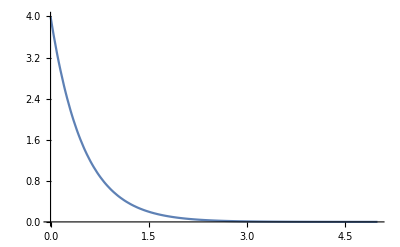

```mathematica
plotRa=Plot[R[1,0,x],{x,0,5},PlotRange->All]
```

```mathematica
temp=NDEigensystem[{Subscript[ℋ, 2][ψ[x,y]],Subscript[ℬ, 2]},ψ[x,y],{x,y}∈Subscript[ℛ, 2]/.{Rin->0.001,Rout->5},70,Method->{"Eigensystem"->{"Arnoldi","MaxIterations"->100}}(*,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.1}}}}*)];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 100, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

```mathematica
temp2=SortBy[Transpose[temp],First];
temp[[1,1]]
```

-0.131764

```mathematica
Plot3D[temp2[[2,2]],Evaluate[{x,y}∈Subscript[ℛ, 2]/.{Rin->0.001,Rout->20}],PlotRange->All,PlotPoints->50 ]
```

-Graphics3D-

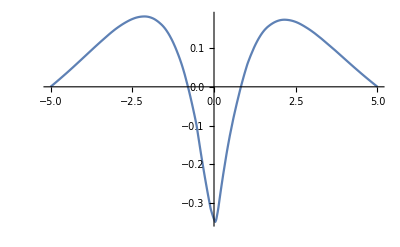

```mathematica
plotRn=Plot[temp2[[4,2]]/.y->0,{x,-20,20},PlotRange->All ]
```

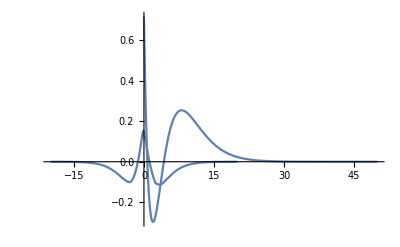

```mathematica
Show[plotRa,plotRn]
```

Calculation of the 4 lowest energy eigenstates of the Hydrogen atom for different choices  of the calculation box ℓ, and the size of the spatial discretization Δx.

```mathematica
(*Manipulate[
Table[Plot[#⟦i,2⟧/.x->0,{y,-rout,rout},PlotPoints->25,PlotRange->All,PlotLabel->StringTemplate["E_(``) = `` (``)"][i,#⟦i,1⟧,Subscript[ℰ, 2]⟦i⟧]],{i,1,2}]&@SortBy[Transpose[NDEigensystem[{Subscript[ℋ, 2][ψ[x,y]],Subscript[ℬ, 2]},ψ[x,y],{x,y}∈Evaluate[Subscript[ℛ, 2]/.{Rin->rin,Rout->rout}],50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->Δx}}}}]],First],"Rin"->{rin,0.0001,0.1,0.01},"Rout"-> {rout,5,15,1},"Δx"->{Δx,0.01,0.11,0.05}]*)
```

```mathematica
(*Manipulate[
Table[Plot3D[#⟦i,2⟧,{x,y}∈Evaluate[Subscript[ℛ, 2]/.{Rin->rin,Rout->rout}],PlotPoints->25,PlotRange->All,PlotLabel->StringTemplate["E_(``) = `` (``)"][i,#⟦i,1⟧,Subscript[ℰ, 2]⟦i⟧]],{i,1,1}]&@SortBy[Transpose[NDEigensystem[{Subscript[ℋ, 2][ψ[x,y]],Subscript[ℬ, 2]},ψ[x,y],{x,y}∈Evaluate[Subscript[ℛ, 2]/.{Rin->rin,Rout->rout}],50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->Δx}}}}]],First],"Rin"->{rin,0.001,0.1,0.01},"Rout"-> {rout,4,10,0.25},"Δx"->{Δx,0.01,0.11,0.05}]*)
```

## ns as needed to explain the topic (cmd/alt+4)

Section names, the total number of sections, and section organization will differ based on the topic.

Here are some ideas for sections you might consider:

history/origins
derivation
applications
common misunderstandings
recent developments
unanswered questions

Further Explorations

Name of a related topic for exploration

Name of another related topics for exploration (repeat as needed)

Authorship information

Name of Author

Date of creation

Author email address (please use the email associated with your Wolfram User ID)

PredictiveInterface`DoPredictionAction::newsess: Suggested actions are only available in the same kernel session that suggested them.